```mathematica
-Graphics-;
```

In order to cover the moduli space with globally dense packings, we need to look at what happens in the regions in the moduli space where free circles exist.  We can do this by taking the two edge cases, the purple edge above the red region and the blue line above the yellow region and taking these packings and simply extending the length of the lattice vector w1 or w2.  In this document, we will look at the region that is encapsulated above the yellow region, which is found by extending the packings that are on the blue line (the blue line that is directly above the yellow region).

We start off by taking the centers of the embedding V3E6L1N2T11 as below.

```mathematica
centers = {{0,0},{(1/Sqrt[2])*Cos[α],(1/Sqrt[2])*Sin[α]},{(1/Sqrt[2])*Cos[-α]+((2/Sqrt[2])(Cos[π/4]))*Cos[π/4+α],(1/Sqrt[2])*Sin[-α]+((2/Sqrt[2])(Cos[π/4]))*Sin[π/4+α]}}
```

{{0,0},{Cos[α]/(√2),Sin[α]/(√2)},{Cos[α]/(√2)+Cos[π/4+α],-Sin[α]/(√2)+Sin[π/4+α]}}

Then we take the lattice vectors of the embedding V3E6L1N2T11.  However, note that we take the longer lattice vector, in this case w1 and scale it by some factor t.

```mathematica
latticeVectors = {
 {t((2/Sqrt[2])*Cos[α]),0},
{ ((2 /√2 )*Cos[π/4] )*Cos[α+π/4],((2 /√2 )*Cos[π/4] )*Sin[α+π/4]}};
```

Also, to allow free circles, we need to break some of the edges.  These are the remaining edges we keep so that we can visualize the packing.

```mathematica
edges = {{1,2,0,0},{1,1,0,1},{2,1,0,1},{3,1,0,1}};
```

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,t->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,t->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,t->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,t->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,t->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,t->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,t->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,t->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[1]]/.{α->a,t->b},Offset[{0,10},{0,0}]]},
{Text[Style["t",Small],centers[[1]]/.{α->a,t->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,t->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,.4,"α"},π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{{b,1,"t"},1,1/(2*Cos[a+Pi/4]*((2/Sqrt[2])*Cos[a]))}]
```

Now, we know that as we scale the lattice vector by t, the x coordinate cannot be greater than 1/2.  So, using trigonometry with a right triangle, we get the upper bound on t as: 1/(2*Cos[a+Pi/4]*((2/Sqrt[2])*Cos[a])).  Obviously, our lower bound on t is 1 because that corresponds to the edge we already have.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α,t},Reals],t>1,π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

π/4+α

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[1]]]/EuclideanDistance[{0,0},latticeVectors[[2]]],{Element[{α},Reals],t>0,π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

√2 t Cos[α]

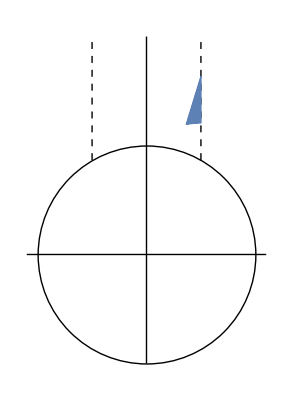

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{torusRatio*Cos[ torusAngleFromVectors],torusRatio*Sin[ torusAngleFromVectors]},{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{t,1,1/(2*Cos[α+Pi/4]*((2/Sqrt[2])*Cos[α]))}]
]
```

So this is the region where free circles exist that roughly corresponds to the embedding V3E6L1N2T11.

## Density Of Packings

Here we analyze the density of the packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α},Reals],t>0,π/8<α<1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4}]
```

-((-7+4 √2) π Sec[α])/(4 t (Cos[α]+Sin[α]))

Plot the density over the parameter space

```mathematica
Plot3D[torusDensity,{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{t,1,1/(2*Cos[α+Pi/4]*((2/Sqrt[2])*Cos[α]))},AxesLabel->Automatic]
```

-Graphics3D-

-Graphics3D-

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

```mathematica
ParametricPlot3D[{torusRatio*Cos[ torusAngleFromVectors],torusRatio*Sin[ torusAngleFromVectors],torusDensity},{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{t,1,1/(2*Cos[α+Pi/4]*((2/Sqrt[2])*Cos[α]))},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{torusRatio*Cos[ torusAngleFromVectors],torusRatio*Sin[ torusAngleFromVectors],(torusDensity)},{α,π/8,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4},{t,1,1/(2*Cos[α+Pi/4]*((2/Sqrt[2])*Cos[α]))},PlotStyle->Blue,Mesh->None]
```

-Graphics3D-